```mathematica
f[y_]:=Module[{dydx,tps},dydx=D[y,x];tps={x,y}/.Solve[dydx==0,x,Reals];Plot[y,{x,-3,3}, Epilog->{Point[tps]}]]
```

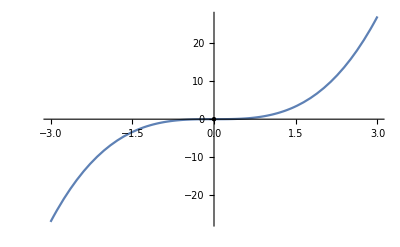

```mathematica
f[x^3]
```